Procedimento para calcular a metragem cúbica (volume) que obterá de um tronco após o “corte”.

1) Estimar o ponto central (longitudinal) do tronco.

2) Medir a circunferência naquele ponto.

O comprimento do círculo naquele ponto.
Vamos supor uma medida m=12. Não podemos supor uma medida pois o procedimento começa medindo a medida de um círculo (que não pode ser desenhado pelo comprimento). Precisamos, também, medir um círculo arbitrário.
Comprimento do círculo = 2π·R.
O comprimento medido foi m=47.69.

3) Dividir a circunferência por quatro.

Aqui, o comprimento de um quarto do círculo.
m_2=3.

```mathematica
47.69/4
```

11.9225

4) Elevar isto ao quadrado.

Isto é montar um quadrado com lado igual a este comprimento (“esticado”). GeoGebra.
A área do quadrado é m_3=9.
Como estamos estabelecendo o quadrado pela medida e não geometricamente, seria interessante comparar geometricamente este quadrado com o círculo.

5) Multiplicar isto pela altura do tronco (obtendo o “volume”).

Calcularei a altura do cone a partir da diferença no raio entre a base e o topo do tronco e a altura do tronco.
Se a base tem raio 0.5 e o topo, 0.2, e o tronco tem 9 de altura...
A razão entre topo e raio é 0.2/0.5=0.2/(1/2)=0.2·2=0.4.
Quando o topo será 0? Em 9 m, o raio caiu de 0.5 a 0.2. Mas essa é uma relação linear, uma subtração. O raio caiu 0.3 (e não uma porcentagem do raio original) em 9.
Em quanto o raio cairá mais 0.2? 0.2/0.3=x/9⇒0.3x=1.8⇒x=6.
Então a altura do cone é 9+6=15.
Ou R_t/R_b=(h_c-h_t)/h_t⇒
(h_c-h_t) R_b=R_t h_t⇒
h_c-h_t=(R_t h_t)/R_b⇒
h_c=(R_t h_t)/R_b+h_t=((R_t h_t)+(h_t R_b))/R_b=(h_t (R_t+R_b))/R_b.
Onde:
R_t = raio do tronco
R_b = raio da base
h_c = altura do cone (completo)
h_t = altura do tronco
Testando.

```mathematica
(9*(0.2+0.5))/0.5
```

12.6

Obter o volume do cone desta altura com mesma base (cone completo), obter o volume do cone de base R_t e altura h_2=h_c-h_t, e subtrair o volume do primeiro pelo do segundo.

O volume do cone (Geometria II p. 204) é (π·r^2·h)/3, em que r é o raio e h altura.

Cone completo:
Primeiro, a altura do cone...

```mathematica
Clear[ConeAlt];
ConeAlt=Function[{htronco,Rtopo,Rb},(htronco*(Rtopo+Rb))/Rb];
```

```mathematica
ConeAlt[9,0.2,0.5]
```

12.6

O volume do cone completo...

```mathematica
Clear[ConeVol];
ConeVol=Function[{r,h},(π*r^2*h)/3];
```

```mathematica
ConeVol[0.5,12.6]
```

3.29867

O volume do cone topo...

```mathematica
ConeVol[0.2,12.6-9]
```

0.150796

Subtração dos volumes.

```mathematica
ConeVol[0.5,ConeAlt[9,0.2,0.5]]-ConeVol[0.2,ConeAlt[9,0.2,0.5]-9]
```

3.14788

Este é o volume do “tronco do cone”.
Agora, como unir isto em uma função?

Função do volume de um tronco de cone. Estas são medidas do tronco (de cone). A altura é, coincidentemente, igual à do tronco (de madeira).

V(r_b,r_t,h)=ConeVol[r_b,(h·(r_b+r_t))/r_b]-ConeVol[r_t,(h·(r_b+r_t))/r_b-h]=
(π·r_b^2·(h·(r_b+r_t))/r_b·1/3)-[π·r_t^2·((h·(r_b+r_t))/r_b-h)·1/3]=
(π·r_b^2·(h·(r_b+r_t))/(3 r_b))-[π·r_t^2·(h·(r_b+r_t)-h·r_b)/(3 r_b)]=
(3r_b·π·3r_b^3·h·(r_b+r_t))/(3 r_b)-(3r_b·π·3 r_b r_t^2·h·(r_b+r_t-r_b))/(3 r_b)=
9r_b^4·π·h·(r_b+r_t)-9r_b^2·π·r_t^2·h·r_t.

```mathematica
Clear[ConeTVolM];
ConeTVolM=Function[{rb,rt,h},9*rb^4*π*h*(rb+rt)-9*rb^2*π*rt^2*h*rt];
```

```mathematica
ConeTVolM[0.5,0.2,9]
```

10.6241

```mathematica
ConeTVol=Function[{rb,rt,h},ConeVol[rb,ConeAlt[h,rt,rb]]-
	ConeVol[rt,ConeAlt[h,rt,rb]-h]];
```

```mathematica
ConeTVol[rb,rt,h]
```

1/3 h π rb (rb+rt)-1/3 π rt^2 (-h+(h (rb+rt))/rb)

```mathematica
Simplify[1/3 h π rb (rb+rt)-1/3 π rt^2 (-h+(h (rb+rt))/rb)]
```

(h π (rb^3+rb^2 rt-rt^3))/(3 rb)

```mathematica
ConeTVol[0.5,0.2,9]
```

3.14788

Vamos por partes.

```mathematica
ConeVol[rb,(h*(rb+rt))/rb]
```

1/3 h π rb (rb+rt)

ConeVol[r_b,(h·(r_b+r_t))/r_b]=1/3·π·r_b^2·(h·(r_b+r_t))/r_b=
1/3·π·r_b·h·(r_b+r_t).

Entendi, tudo.
(h = altura do tronco de cone.)

V(r_b,r_t,h)=
(π r_b^2·(h (r_b+r_t))/r_b·1/3)-π r_t^2 ((h (r_b+r_t))/r_b-h)·1/3=
1/3 π r_b·h (r_b+r_t)-1/3 π r_t^2 ((h (r_b+r_t)-h r_b)/r_b)=
1/3 π r_b·h (r_b+r_t)-1/3 π r_t^2·(h r_t)/r_b=
1/3 π [r_b h (r_b+r_t)-r_t^2·(h r_t)/r_b]=
1/3 π [(r_b^2 h (r_b+r_t)-r_t^2 h r_t)/r_b]=
(π h (r_b^2 (r_b+r_t)-r_t^3))/(3 r_b)=
(π h (r_b^3+r_b^2 r_t-r_t^3))/(3 r_b).

```mathematica
Clear[ConeTVolM];
ConeTVolM=Function[{rb,rt,h},1/3*π*(h*(rb^3+rb^2*rt-rt^3))/rb];
```

```mathematica
ConeTVolM[0.5,0.2,9]
```

3.14788

```mathematica
(π 9 (0.5^2 0.7 -0.2^3))/(3 0.5)
```

3.14788

Então, se for pela média (meio do tronco) para o cilindro, este teria raio:

```mathematica
0.2+(0.5-0.2)/2
```

0.35

E volume:

```mathematica
0.35^2*π*9
```

3.46361

```mathematica
3.4636059005827464-3.14788
```

0.315726

Seria esta diferença linear com o aumento das dimensões das bases e altura do tronco?

```mathematica
Clear[MediumVol]
MediumVol=Function[{rb,rt,h},((rb+rt)/2)^2*π*h];
```

Altura do tronco de 1 a 50...

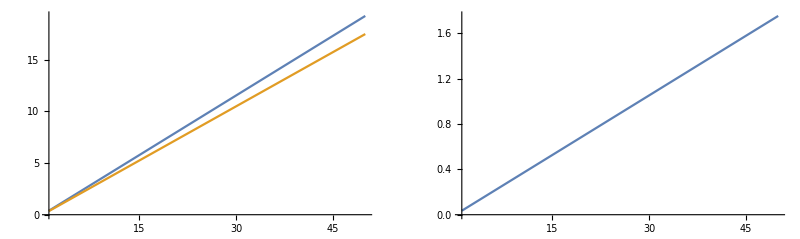

```mathematica
Module[{rb,rt},rb=0.5;rt=0.2;
GraphicsRow[{
Plot[{MediumVol[rb,rt,h],ConeTVolM[rb,rt,h]},{h,1,50}],
Plot[MediumVol[rb,rt,h]-ConeTVolM[rb,rt,h],{h,1,50}]
}]
]
```

Raios mais diferentes?

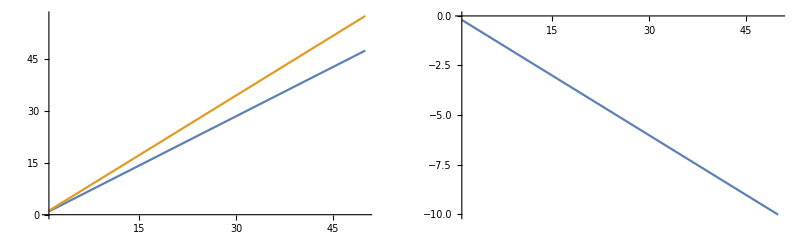

```mathematica
Module[{rb,rt},rb=1;rt=0.1;
GraphicsRow[{
Plot[{MediumVol[rb,rt,h],ConeTVolM[rb,rt,h]},{h,1,50}],
Plot[MediumVol[rb,rt,h]-ConeTVolM[rb,rt,h],{h,1,50}]
}]
]
```

Mesma diferença, medida deslocada?

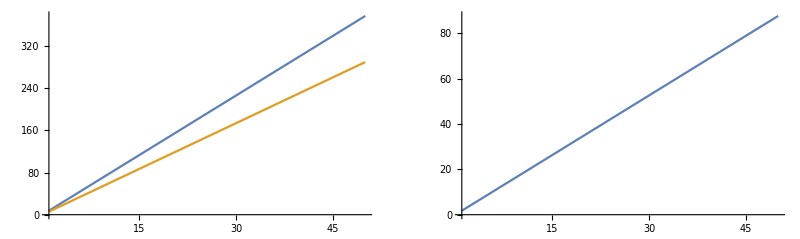

```mathematica
Module[{rb,rt},rb=2;rt=1.1;
GraphicsRow[{
Plot[{MediumVol[rb,rt,h],ConeTVolM[rb,rt,h]},{h,1,50}],
Plot[MediumVol[rb,rt,h]-ConeTVolM[rb,rt,h],{h,1,50}]
}]
]
```

Ou seja, não é só diferença, quanto maiores os raios (e também a diferença), maior a discrepância... Reverificar.

Antes das derivadas...

Variando r_b.

```mathematica
Manipulate[Plot[{MediumVol[rb,rt,h],ConeTVolM[rb,rt,h]},{h,0,10}],{{rb,.5},0,3,.01,Appearance->"Labeled"},{{rt,.2},0,2,.01,Appearance->"Labeled"}]
```

MediumVol: volume do cilindro tomado pelo raio na média entre o raio da base e do topo.
ConeTVolM: volume do tronco do cone com raios base e topo.
Ambos de mesma altura.
Todo:
Marcar o valor das duas funções em h=9.
Restringir r_t≥r_b.

Comparações manuais (GeoGebra).
A função do volume do cilindro estava errada?

```mathematica
{MediumVol[33.49,23.58,10.6], ConeTVolM[33.49,23.58,10.6]}
```

{27115.1,16870.1}

O volume do cilindro (Geometria II p. 193) é π r^2 h, não r h.

Função diferença.

```mathematica
ConeTVolM[rb,rt,h]-MediumVol[rb,rt,h]
```

-1/4 h π (rb+rt)^2+(h π (rb^3+rb^2 rt-rt^3))/(3 rb)

```mathematica
Simplify[ConeTVolM[rb,rt,h]-MediumVol[rb,rt,h]]
```

(h π (rb^3-2 rb^2 rt-3 rb rt^2-4 rt^3))/(12 rb)

### Derivadas

Seria legal descobrir a função discrepância e achar o máximo e mínimo.
O problema é que são três variáveis. Mas podemos achar as derivadas parciais.

Dessa forma, a função discrepância é apenas a subtração combinada das duas medidas.

```mathematica
Simplify[MediumVol[rb,rt,h]-ConeTVolM[rb,rt,h]]
```

(h π (-rb^3+2 rb^2 rt+3 rb rt^2+4 rt^3))/(12 rb)

```mathematica
Clear[Discr]
Discr=MediumVol[rb,rt,h]-ConeTVolM[rb,rt,h]
```

1/4 h π (rb+rt)^2-(h π (rb^3+rb^2 rt-rt^3))/(3 rb)

```mathematica
Clear[DiscrRb,DiscrRt,DiscrH];
DiscrRb[rb_,rt_,h_]=D[Discr, rb];
DiscrRt[rb_,rt_,h_]=D[Discr, rt];
DiscrH[rb_,rt_,h_]=D[Discr, h];
Head[DiscrRb];
DiscrRb;
DiscrRb[rb,rt,h];
DiscrRb[rb,0.5,10];
```

```mathematica
DiscrRb[rb,rt,h]
DiscrRt[rb,rt,h]
DiscrH[rb,rt,h]
```

1/2 h π (rb+rt)-(h π (3 rb^2+2 rb rt))/(3 rb)+(h π (rb^3+rb^2 rt-rt^3))/(3 rb^2)

1/2 h π (rb+rt)-(h π (rb^2-3 rt^2))/(3 rb)

1/4 π (rb+rt)^2-(π (rb^3+rb^2 rt-rt^3))/(3 rb)

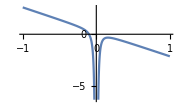
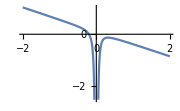
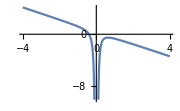

```mathematica
{
Plot[{DiscrRb[rb,0.1,4.5]},{rb,-1,1},ImageSize->Small],
Plot[{DiscrRb[rb,0.2,0.9]},{rb,-2,2},ImageSize->Small],
Plot[{DiscrRb[rb,0.4,1.8]},{rb,-4,4},ImageSize->Small]
}
```

```mathematica
N[Solve[DiscrRb[rb,0.1,4.5]==0]]
N[Solve[DiscrRb[rb,0.2,0.9]==0]]
N[Solve[DiscrRb[rb,0.4,1.8]==0]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{rb→-0.1},{rb→0.1-0.1 ⅈ},{rb→0.1+0.1 ⅈ}}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{rb→-0.2},{rb→0.2-0.2 ⅈ},{rb→0.2+0.2 ⅈ}}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{rb→-0.4},{rb→0.4-0.4 ⅈ},{rb→0.4+0.4 ⅈ}}

Só tem solução negativa. O que isso quer dizer?

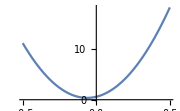
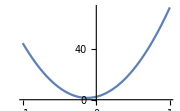
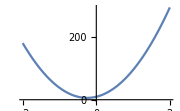

```mathematica
{
Plot[{DiscrRt[0.25,rt,4.5]},{rt,-0.5,0.5},ImageSize->Small],
Plot[{DiscrRt[0.5,rt,9]},{rt,-1,1},ImageSize->Small],
Plot[{DiscrRt[1,rt,18]},{rt,-2,2},ImageSize->Small]
}
```

```mathematica
N[Solve[DiscrRt[0.25,rt,4.5]==0]]
N[Solve[DiscrRt[0.5,rt,9]==0]]
N[Solve[DiscrRt[1,rt,18]==0]]
```

{{rt→-0.0625-0.0806872 ⅈ},{rt→-0.0625+0.0806872 ⅈ}}

{{rt→-0.125-0.161374 ⅈ},{rt→-0.125+0.161374 ⅈ}}

{{rt→-0.25-0.322749 ⅈ},{rt→-0.25+0.322749 ⅈ}}

Só tem solução complexa.

Plotar a antiderivada. (?)

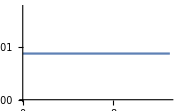
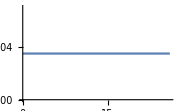
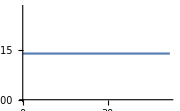

```mathematica
{
Plot[{DiscrH[0.25,0.1,h]},{h,0,13},ImageSize->Small],
Plot[{DiscrH[0.5,0.2,h]},{h,0,26},ImageSize->Small],
Plot[{DiscrH[1,0.4,h]},{h,0,52},ImageSize->Small]
}
```

Essa ausência de soluções indica que as variáveis não têm mínimos.

As três parciais (cada uma em uma variável) foram um sistema de três equações em três variáveis para resolver?

#### GeoGebra

A circunscrição do hexágono no círculo foi feita da seguinte forma (Cubagem3.ggb):
- Foi definido o ponto central do círculo;
- Foi medido o raio de um ponto no círculo ao ponto central e traçado um segundo círculo do ponto no círculo passando pelo ponto central, cruzando o primeiro círculo (compasso)
- No ponto de cruzamento, foi traçado outro círculo com o mesmo raio e cruzando o primeiro círculo novamente
- E assim sucessivamente até seccionar o círculo em seis arcos.
- Foi traçado o hexágono unindo os seis pontos.

Fontes:
Geometria I e II - Disciplina na modalidade a distância - Unisul Virtual, 2011
Kelen Regina Salles Silva e Christian Wagner.

Circunscrição do hexágono no círculo: Geometria I págs. 48 e 61
Área do hexágono regular: Geometria I pág. 168
Área do círculo: Geometria I pág. 183
Volume do cone: Geometria II pág. 204